# Entanglement Entropy for the XY model

## Dof and Precision

```mathematica
nn=551;
prec=2020;
```

## Hamiltonian

### Matrix A

```mathematica
Clear[a0,a1,a2]
Α= Table[ If[i==j,a0,If[Mod[i-j,nn]==1,a2,If[Mod[j-i,nn]==1,a1,0]]],{i,1,nn},{j,1,nn}];
γ=1/2//N[#,prec]&;
λ=1/2//N[#,prec]&;
a0=λ//N[#,prec]&;
a1=(1-γ)/2//N[#,prec]&;
a2=(1+γ)/2//N[#,prec]&;
```

```mathematica
Α//N[#,4]&//MatrixForm
```

(1)
 |  |  |  |

### Frequencies

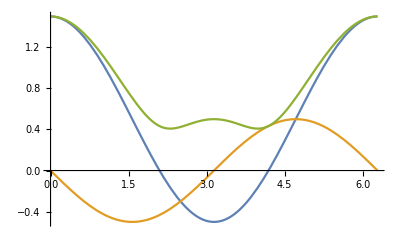

```mathematica
α[θ_]:=(a0+(a2+a1) Cos[θ]);
β[θ_]:=(a1-a2) Sin[θ];
ω[θ_]:=√(α[θ]^2+β[θ]^2);
Plot[{α[x],β[x],ω[x]},{x,0,2 π}]
```

### Matrix B

```mathematica
b[l_]:={{α[(2 π l)/nn],-β[(2 π l)/nn]},{β[(2 π l)/nn],α[(2 π l)/nn]}}
bhat[l_]:=1/ω[(2 π l)/nn] {{α[(2 π l)/nn],-β[(2 π l)/nn]},{β[(2 π l)/nn],α[(2 π l)/nn]}}
B=ConstantArray[0,{nn,nn}];
B⟦1,1⟧=N[α[0],prec];
B⟦nn,nn⟧=N[α[π],prec];
Table[
B⟦2 k;;1+2 k,2 k;;1+2 k⟧=N[b[k],prec];,
{k,1,nn/2-1}];
(*B//MatrixForm;*)
Bhat=ConstantArray[0,{nn,nn}];
Bhat⟦1,1⟧=N[α[0]/ω[0],prec];
Bhat⟦nn,nn⟧=N[ α[π]/ω[π],prec];
Table[
Bhat⟦2 k;;1+2 k,2 k;;1+2 k⟧=N[bhat[k],prec];,
{k,1,nn/2-1}];
```

```mathematica
Bhat//N[#,4]&//MatrixForm
```

(1)
 |  |  |  |

## Diagonalization

### RDFT

```mathematica
(*
Ω=E^(I (2 π)/nn);
v1=Table[Ω^k,{k,0,nn-1}];
(U=Table[v1^l/Sqrt[nn],{l,0,nn-1}])//MatrixForm;
Ort=Flatten[Table[Sqrt[2] {Im[U][[i]],Re[U][[i]]},{i,2,nn/2}],1];
(Ortt=Insert[Ort,Re[U][[1]],1])//MatrixForm;
(Orttt=Insert[Ortt,Re[U][[nn/2+1]],nn])//MatrixForm;
*)
OFourier=ConstantArray[0,{nn,nn}];
Table[If[l>1,
OFourier⟦l+1,k+1⟧=N[√(2/nn) Cos[(π l)/nn k],prec],
OFourier⟦1,k+1⟧=N[√(1/nn) Cos[(π l)/nn k],prec]],
{l,0,nn-1,2},{k,0,nn-1}];
Table[
If[l<nn-2,
OFourier⟦l+2,k+1⟧=N[√(2/nn) Sin[(2 π (l/2+1))/nn k],prec],
OFourier⟦nn,k+1⟧=N[√(1/nn) Cos[π k],prec]],
{l,0,nn-1,2},{k,0,nn-1}];
(*
OFourier//MatrixForm;
OFourier.Transpose[OFourier]//MatrixForm//Chop[#,10^(-prec+1)]&;
*)
(*
(QFourier=ArrayFlatten[{{OFourier,0},{0,OFourier}}])//MatrixForm;
(A=ArrayFlatten[{{0,Α},{-Transpose[Α],0}}])//MatrixForm;
*)
(*
OFourier.Α.Transpose[OFourier]//MatrixForm//Chop[#,10^(-prec+1)]&;
OFourier.Transpose[Α].Transpose[OFourier]//MatrixForm//Chop[#,10^(-prec+1)]&;
B//MatrixForm;
QFourier.A.Transpose[QFourier]//MatrixForm//Chop[#,10^(-prec+1)]&;
*)
```

### Full Transformation

```mathematica
(*
(Q2=ArrayFlatten[{{Transpose[B1hat],0},{0,IdentityMatrix[nn]}}])//MatrixForm;
*)
(*
bigO=Q2.QFourier;
bigO.Transpose[bigO]//MatrixForm//Chop[#,10^(-prec+1)]&;
*)
(*
(W=bigO.A.Transpose[bigO])//MatrixForm//Chop[#,10^(-prec+1)]&;
*)
(o1=(Bhat//Transpose).OFourier)//MatrixForm;
(o2=(OFourier//Transpose))//MatrixForm;
(*
o1.Α.o2//MatrixForm//Chop[#,10^(-prec+2)]&;
*)
```

```mathematica
o1//N[#,4]&//MatrixForm
```

(1)
 |  |  |  |

```mathematica
o2//N[#,4]&//MatrixForm
```

(1)
 |  |  |  |

```mathematica
o1.Α.o2//MatrixForm//N[#,4]&//Chop[#,10^(-prec+2)]&
```

(1)
 |  |  |  |

### Entanglement Entropy

#### Ground State

```mathematica
MGSDiag= Table[ If[i==j,1/2,0],{i,1,nn},{j,1,nn}];
(MGSEsp=Transpose[o1].MGSDiag.Transpose[o2])//MatrixForm;
lmaxGS=IntegerPart[nn/10];
GSentab=Table[ 
MGSEspRed = Take[ Take[#,l]& /@ MGSEsp, l];
GSSVLocal= (SingularValueDecomposition[MGSEspRed]⟦2⟧//Diagonal)//Flatten;
GSentropy=Plus@@(-(# +1/2)Log[(# +1/2)]- (-# +1/2)Log[(-# +1/2)]& /@ GSSVLocal);
{l,GSentropy},
{l,1,lmaxGS}];
GSsplot=GSentab//ListPlot;
Manipulate[GSteoplot=Plot[r1 Log[2,l]+r2,{l,0,lmaxGS}];
Show[GSsplot,GSteoplot],{{r2,0},-10,10},{r1,0,1}]
fit=NonlinearModelFit[GSentab⟦All,2⟧,q1 Log[2,l]+q2,{q1,q2},l]
```

FittedModel[(«559»-«557» ⅈ)+(«559»+«557» ⅈ) Log[l]]

#### Random Excited State

General::munfl: Exp[-500000.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

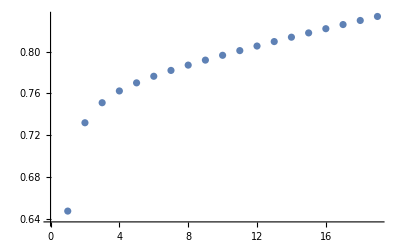

```mathematica
Manipulate[Plot[1/(E^(a (x-μ1))+1),{x,0,10}],{a,0,10},{μ1,0,4}];
βT=1000000/1//N[#,prec]&;
μ=2//N[#,prec]&;
p[l_]:=1/(E^(βT (ω[(2 π)/nn l]-μ))+1)
prob=Plot[p[x],{x,0,nn-1}];
MDiag= Table[ If[i==j,If[RandomReal[]>p[i],-1/2,1/2],0],{i,1,nn},{j,1,nn}];
MDiag//MatrixForm;
(MEsp=Transpose[o1].MDiag.Transpose[o2])//MatrixForm;
lmax=IntegerPart[nn/10];
entab=Table[ 
MEspRed = Take[ Take[#,l]& /@ MEsp, l];
SVLocal= (SingularValueDecomposition[MEspRed]⟦2⟧//Diagonal)//Flatten;
entropy=Plus@@(-(# +1/2)Log[(# +1/2)]- (-# +1/2)Log[(-# +1/2)]& /@ SVLocal);
{l,entropy},
{l,1,lmax}];
splot=entab//ListPlot
```

## Spatial Structure of Enetanglement Entropy

### Participation Function

```mathematica
ll=IntegerPart[nn/10];
MEspRed1 = Take[ Take[#,ll]& /@ MEsp, ll];
SVD=SingularValueDecomposition[MEspRed1];
ρ=1/2 ((SVD⟦1⟧)^2+(SVD⟦3⟧)^2);
```

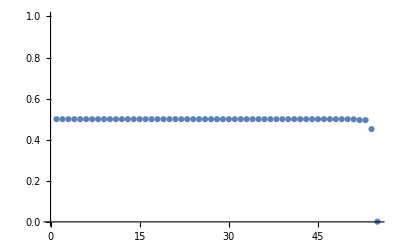

-Graphics3D-

```mathematica
ListLinePlot[Table[ρ⟦All,i⟧,{i,1,ll}],ImageSize->Large,PlotRange->All];
SVD⟦2⟧//Diagonal//ListPlot
ListPlot3D[ρ,PlotRange->All,ImageSize->Large]
```

```mathematica
Manipulate[ListLinePlot[ρ⟦All,i⟧,ImageSize->Medium,PlotRange->All,PlotLabel->(s@SVD[[2,i,i]]//N)],{i,1,Length[MEspRed1]}]
```

### Entanglement Spectrum

```mathematica
s[x_] =-( 1/2-x) Log[2,1/2-x] -( 1/2+x) Log[2,1/2+x] ;
```

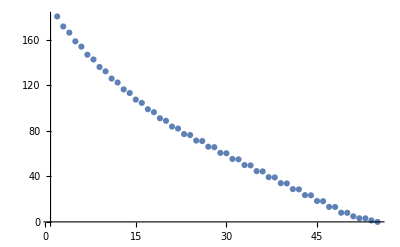

```mathematica
(EntSpecRest=(s/@(SVD⟦2⟧//Diagonal)) //-Log[#]&)//ListPlot[#,PlotRange->All]&
```

## Hamiltonian (small system)

### Matrix A (small system)

```mathematica
Αs= Table[ If[i==j,a0,If[Mod[i-j,ll]==1,a2,If[Mod[j-i,ll]==1,a1,0]]],{i,1,ll},{j,1,ll}];
```

### Matrix B (small system)

```mathematica
bs[l_]:={{α[(2 π l)/ll],-β[(2 π l)/ll]},{β[(2 π l)/ll],α[(2 π l)/ll]}}
bhats[l_]:=1/ω[(2 π l)/ll] {{α[(2 π l)/ll],-β[(2 π l)/ll]},{β[(2 π l)/ll],α[(2 π l)/ll]}}
Bs=ConstantArray[0,{ll,ll}];
Bs⟦1,1⟧=N[α[0],prec];
Bs⟦ll,ll⟧=N[α[π],prec];
Table[
Bs⟦2 k;;1+2 k,2 k;;1+2 k⟧=N[bs[k],prec];,
{k,1,ll/2-1}];
(*B//MatrixForm;*)
Bhats=ConstantArray[0,{ll,ll}];
Bhats⟦1,1⟧=N[α[0]/ω[0],prec];
Bhats⟦ll,ll⟧=N[ α[π]/ω[π],prec];
Table[
Bhats⟦2 k;;1+2 k,2 k;;1+2 k⟧=N[bhats[k],prec];,
{k,1,ll/2-1}];
```

## Diagonalization (small system)

### RDFT (small system)

```mathematica
OFouriers=ConstantArray[0,{ll,ll}];
Table[If[l>1,
OFouriers⟦l+1,k+1⟧=N[√(2/ll) Cos[(π l)/ll k],prec],
OFouriers⟦1,k+1⟧=N[√(1/ll) Cos[(π l)/ll k],prec]],
{l,0,ll-1,2},{k,0,ll-1}];
Table[
If[l<ll-2,
OFouriers⟦l+2,k+1⟧=N[√(2/ll) Sin[(2 π (l/2+1))/ll k],prec],
OFouriers⟦ll,k+1⟧=N[√(1/ll) Cos[π k],prec]],
{l,0,ll-1,2},{k,0,ll-1}];
```

### Full Transformation (small system)

```mathematica
(o1s=(Bhats//Transpose).OFouriers)//MatrixForm;
(o2s=(OFouriers//Transpose))//MatrixForm;
(*
o1s.Αs.o2s//MatrixForm//Chop[#,10^(-prec+2)]&;
*)
```

### Entanglement Spectrum (small system)

```mathematica
(*
SVDs=SingularValueDecomposition[Αs];
EntSpecSmallPlot=(s/@(SVDs⟦2⟧//Diagonal)) //-Log[#]&//ListLinePlot[#,PlotRange->All]&
*)
```

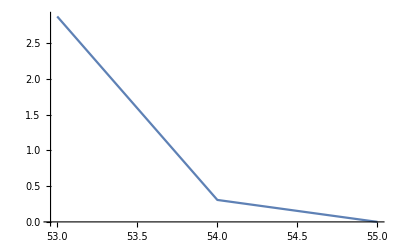

```mathematica
(MSmallDiag=Take[ Take[#,ll]& /@ MDiag, ll])//N[#,2]&//MatrixForm;
(MEspSmall=Transpose[o1s].MSmallDiag.Transpose[o2s])//N[#,2]&//MatrixForm;
(EntSpecSmall=(s/@(SingularValueDecomposition[MEspSmall]⟦2⟧//Diagonal))//-Log[#]&)//ListLinePlot[#,PlotRange->All]&
```

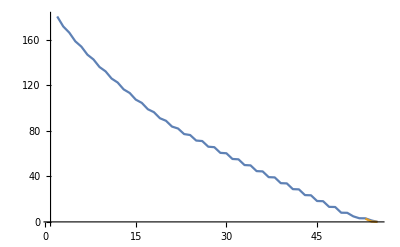

```mathematica
ListLinePlot[{EntSpecRest,EntSpecSmall},PlotRange-> All]
```

```mathematica
s/@(SingularValueDecomposition[MEspSmall]⟦2⟧//Diagonal)
```

{-0.7808016721668140213357630900987018662977857538795419128931586806607134428351624427976674620023921668805861622981971+0.9078309429632380002991517000533570685969561427952260165016888063534823268815956356703717782253921336192688298099388 ⅈ,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,0.0563167012051646070355679359950115325744779452171889572751092133842805021351062977358821777440789113322323543279271,0.7352528945837073252259750199404487864507048559834829836895073424817136263729137920978458252504555093863146448859931,1}